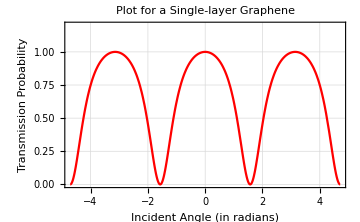

```mathematica
(*Rajdeep Tah, 1911124, Mesoscopic HW-7*)


hbar = 1.0545718*10^(-34); m = 9.10938356*10^(-31); eV = 1.60217662*10^(-19); a = 0.246*10^(-9); 

T[E_, Theta_] := 
 Module[{kx, ky, k, V0 = 0.25, w = 10^(-9)}, 
  kx = Sqrt[(E + V0)*2*m]/hbar*Sin[Theta];
  ky = Sqrt[(E + V0)*2*m]/hbar*Cos[Theta];
  k = Sqrt[kx^2 + ky^2];
  4*kx^2*ky^2/(4*kx^2*ky^2 + (k^2 - ky^2)^2*Sin[k* a *w]^2)]
  
Plot[T[0.3*eV, Theta], {Theta, -3*Pi/2, 3*Pi/2},PlotStyle -> Red,
 Frame -> True,
 FrameLabel -> {"Incident Angle (in radians)", "Transmission Probability"},
 PlotRange -> {All, {0, 1.2}},
 PlotLabel -> "Plot for a Single-layer Graphene",
 ImageSize -> Medium,
GridLines -> Automatic]
```

```mathematica
hbar = 1.0545718*10^(-34); m = 9.10938356*10^(-31); eV = 1.60217662*10^(-19); a = 0.246*10^(-9);
T[E_, Theta_, Phi_] := 
 Module[{kx, ky, k, V0 = 0.2, w = 10^(-9), alpha}, 
  alpha = ArcTan[Cos[Phi], Sin[Phi]/Sqrt[2]];
  kx = Sqrt[(E + V0)*2*m]/hbar*(Cos[Theta]*Cos[alpha] + Sin[Theta]*Sin[alpha]);
  ky = Sqrt[(E + V0)*2*m]/hbar*(Cos[Theta]*Sin[alpha] - Sin[Theta]*Cos[alpha]);
  k = Sqrt[kx^2 + ky^2];
  4*kx^2*ky^2/(4*kx^2*ky^2 + (k^2 - ky^2)^2*Sin[k*a*w]^2)]

Plot3D[T[0.1*eV, Theta, Phi], {Theta, 0, Pi/2}, {Phi, 0, 2*Pi},
 AxesLabel -> {"Incident Angle (in radians)", "Chirality Angle (in radians)", "Transmission Probability"},
 PlotLabel -> "Plot for variation of Transmission Probability for a Single-layer Graphene",
 ImageSize -> Large,ColorFunction -> "TemperatureMap"]
```

-Graphics3D-